```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
changeNK[$N, $K];
```

```mathematica
basis = basisSU[]//Normal;
```

```mathematica
convertToMatrix[suNvec_] := suNvec.(basisSU[]);
```

```mathematica
cMat[tData_] := Module[{}, (
Table[Join[{tData[[k, 1]]}, convertToMatrix/@Partition[tData[[k,2;;]], ($N)^2-1]], {k, 1, Length[tData]}]
)];
```

```mathematica
TrX2[tpqData_] := Module[{t, Xs}, (
t = tpqData[[1]];
Xs = tpqData[[2;;($K+1)]];

{t, Table[Tr[Xs[[i]].Xs[[j]]]//Chop, {i, 1, $K}, {j, 1, $K}]}
)];
```

```mathematica
TrX3[tpqData_] := Module[{t, Xs}, (
t = tpqData[[1]];
Xs = tpqData[[2;;($K+1)]];

{t, Table[Tr[Xs[[i]].Xs[[j]].Xs[[k]]]//Chop, {i, 1, $K}, {j, 1, $K}, {k, 1, $K}]}
)];
```

```mathematica
TrX4[tpqData_] := Module[{t, Xs}, (
t = tpqData[[1]];
Xs = tpqData[[2;;($K+1)]];

{t, Tr[MatrixPower[Sum[Xs[[i]].Xs[[i]], {i, 1, $K}], 2]]//Chop}
)];
```

```mathematica
data = Import["../../runs/Trials/37754277/86429558.dat"];
```

```mathematica
data2 = Import["../../runs/Trials/68286937/52884929.dat"];
```

```mathematica
matData = cMat[data];
```

```mathematica
matData2 = cMat[data2];
```

```mathematica
trX2  = Monitor[Table[TrX2[matData[[k]]], {k, 1, Length[matData]}], ProgressIndicator[(k-1)/(Length[matData]-1)]];
```

```mathematica
trX3  = Monitor[Table[TrX3[matData[[k]]], {k, 1, Length[matData]}], ProgressIndicator[(k-1)/(Length[matData]-1)]];
```

```mathematica
trX4  = Monitor[Table[TrX4[matData[[k]]], {k, 1, Length[matData]}], ProgressIndicator[(k-1)/(Length[matData]-1)]];
```

```mathematica
trX2  = Monitor[Table[TrX2[matData[[k]]], {k, 1, Length[matData]}], ProgressIndicator[(k-1)/(Length[matData]-1)]];
```

```mathematica
trX3  = Monitor[Table[TrX3[matData[[k]]], {k, 1, Length[matData]}], ProgressIndicator[(k-1)/(Length[matData]-1)]];
```

```mathematica
trX4  = Monitor[Table[TrX4[matData[[k]]], {k, 1, Length[matData]}], ProgressIndicator[(k-1)/(Length[matData]-1)]];
```

```mathematica
Table[Sum[trX3[[t, 2, i, i, k]], {i, 1, $K}], {k ,1, $K}]
```

{0.0726295,0.28294,-0.0377069}

```mathematica
trX2[[6, 2, 1, 2]]
```

0.126881

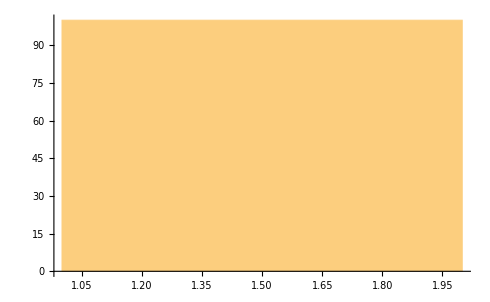

```mathematica
Histogram@Table[1, {k,1, 100}]
```

```mathematica
d = SmoothKernelDistribution[Table[trX2[[t, 2, 1, 2]]//Re, {t, 1 ,Length[trX2]/10}]];
```

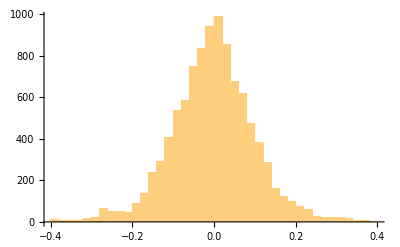

```mathematica
Histogram[Table[trX3[[t, 2, 3, 1, 1]]//Re, {t, 1, Length[trX3]}], 40]
```

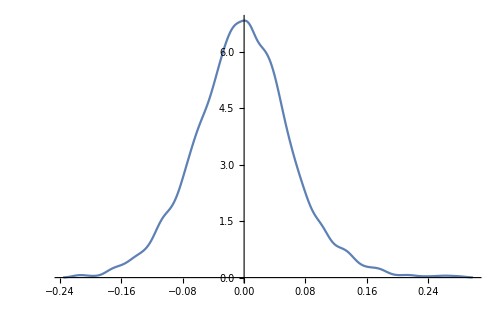
```mathematica
-Graphics-_□
```

```mathematica
Mean[d]
```

-0.010551

```mathematica
StandardDeviation[d]
```

0.233584

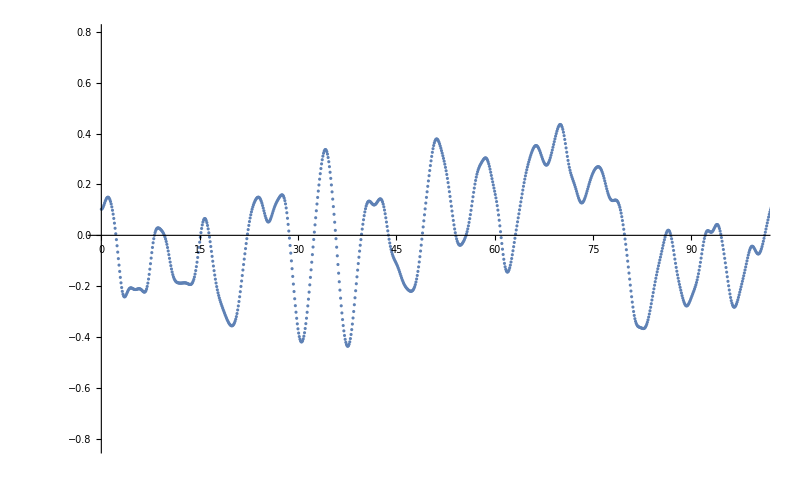

```mathematica
ListPlot[Table[{trX2[[t, 1]],trX2[[t, 2, 1, 2]]//Re}, {t, 1, Length[trX2]}], PlotRange->{{0, 100}, Automatic}]
```

```mathematica
ListPlot[trX4[[All, {1, {1,1,1}}]], PlotRange->{{0,100}, Automatic}]
```

Part::pkspec1: The expression {1,{1,1,1}} cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: trX3⟦All,{1,{1,1,1}}⟧ is not a list of numbers or pairs of numbers.

ListPlot[trX3⟦All,{1,{1,1,1}}⟧,PlotRange→{{0,100},Automatic}]